```mathematica
Clear["Global`*"];
```

```mathematica
B[β_?NumericQ]=(Gamma[(β+2)/2]/Gamma[(β+1)/2])^2;
A[β_?NumericQ]=2/Gamma[(β+1)/2] B[β]^((β+1)/2);
p[s_?NumericQ,β_?NumericQ]:=A[β] s^β ⅇ^(-B[β] s^2)
```

```mathematica
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
NV[L_?NumericQ,ξb_?NumericQ, f_?NumericQ]:= (1-f)L+((ξsb[ξb]/(√ξb))^-2-1) (L/f)^2
```

```mathematica
tablemod[{fileNND_String, fileNV_String, fileL_String}]:=Module[{nnd,filename,nlmNND,nv,nlmNV,l}, 
nnd=Import[fileNND, "Table"];
filename=StringDelete[fileNND,"/home/xierr/Desktop/github_disordered_beta/Chinese/Chinese_NND_results/"|".txt"];
nlmNND=NonlinearModelFit[nnd,p[s,β],β,s];
nv=Import[fileNV, "Table"];
nlmNV=NonlinearModelFit[nv,NV[L,ξb,f],{ξb,f},L];
l=Import[fileL];
{filename,ToExpression[l],N[nlmNND["BestFitParameters"][[1,2]]],N[nlmNV["BestFitParameters"][[2,2]]],N[nlmNV["BestFitParameters"][[1,2]]],N[nlmNND["RSquared"]],N[nlmNV["RSquared"]]}]
```

```mathematica
(*plotmod[file_String]:=Module[{nnd}, 
nnd=Import[file, "Table"];
ListPlot[nnd,PlotMarkers->Automatic]]*)
```

```mathematica
filesNND=FileNames["*.txt","/home/xierr/Desktop/github_disordered_beta/Chinese/Chinese_NND_results"];
filesNV=FileNames["*.txt","/home/xierr/Desktop/github_disordered_beta/Chinese/Chinese_NV_results"];
filesL=FileNames["*.txt","/home/xierr/Desktop/github_disordered_beta/Chinese/Chinese_L_results"];
```

```mathematica
CloseKernels[];LaunchKernels[4];
DistributeDefinitions[tablemod,filesNND,filesNV,filesL];
```

```mathematica
TableForm[ParallelMap[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]},TableHeadings->{None,{"Sequence","⟨L⟩","β","f","ξ̄","R_NND^2","R_NV^2"}}]
```

Sequence | ⟨L⟩ | β | f | ξ̄ | R_NND^2 | R_NV^2
counts_100 | 8.6471 | 1.2238 | 0.7951 | 780.6733 | 0.9705 | 0.9999
counts_101 | 8.5745 | 1.1657 | 0.8030 | 758.9853 | 0.9708 | 1.0000
counts_10 | 6.9862 | 1.7041 | 0.8397 | 2082.7319 | 0.9777 | 0.9997
counts_11 | 6.9974 | 2.3432 | 0.8519 | 627.2206 | 0.9814 | 0.9999
counts_12 | 7.1234 | 2.0524 | 0.8356 | 552.7468 | 0.9611 | 0.9998
counts_13 | 7.0015 | 1.9360 | 0.8465 | 762.4348 | 0.9681 | 0.9998
counts_14 | 7.1988 | 2.1830 | 0.8781 | 975.6073 | 0.9625 | 0.9996
counts_15 | 7.2378 | 1.8401 | 0.8173 | 803.2650 | 0.9709 | 0.9999
counts_16 | 7.2808 | 2.0963 | 0.8268 | 1365.2112 | 0.9739 | 0.9998
counts_17 | 7.0471 | 1.8582 | 0.8334 | 1398.8135 | 0.9795 | 0.9999
counts_18 | 7.2334 | 2.0235 | 0.8071 | 1037.7526 | 0.9651 | 0.9997
counts_19 | 7.3166 | 2.0721 | 0.8175 | 813.8969 | 0.9673 | 0.9998
counts_1 | 7.0077 | 2.0639 | 0.8478 | 1825.1561 | 0.9740 | 0.9996
counts_20 | 7.2444 | 1.8719 | 0.8423 | 1007.4367 | 0.9802 | 0.9999
counts_21 | 7.2629 | 1.9481 | 0.8331 | 1655.3306 | 0.9790 | 0.9999
counts_22 | 7.1057 | 2.1707 | 0.8492 | 778.9123 | 0.9753 | 1.0000
counts_23 | 7.2272 | 2.2764 | 0.8369 | 1721.6081 | 0.9590 | 0.9999
counts_24 | 7.2850 | 1.8938 | 0.8243 | 931.3624 | 0.9742 | 0.9998
counts_25 | 7.1408 | 2.0591 | 0.8352 | 785.0295 | 0.9659 | 0.9999
counts_26 | 7.3150 | 2.1225 | 0.8126 | 1730.6796 | 0.9777 | 0.9996
counts_27 | 7.3338 | 2.0211 | 0.8266 | 1165.0663 | 0.9793 | 0.9998
counts_28 | 7.3554 | 2.2762 | 0.8278 | 846.1098 | 0.9639 | 0.9999
counts_29 | 7.0025 | 1.9569 | 0.8306 | 1303.6957 | 0.9735 | 0.9999
counts_2 | 7.0948 | 2.2399 | 0.8297 | 955.1515 | 0.9661 | 0.9997
counts_30 | 7.3482 | 2.1838 | 0.8114 | 1449.9691 | 0.9743 | 0.9998
counts_31 | 7.1907 | 2.2219 | 0.8358 | 1286.1109 | 0.9675 | 0.9996
counts_32 | 7.2779 | 2.1442 | 0.8318 | 1360.4871 | 0.9713 | 0.9999
counts_33 | 7.2746 | 2.0330 | 0.8218 | 1272.2088 | 0.9667 | 0.9999
counts_34 | 7.1752 | 1.9435 | 0.8476 | 1531.1755 | 0.9726 | 0.9999
counts_35 | 7.2659 | 2.0163 | 0.8286 | 1508.9814 | 0.9851 | 0.9998
counts_36 | 7.2363 | 2.2058 | 0.8459 | 2281.6616 | 0.9792 | 0.9998
counts_37 | 7.0949 | 1.9205 | 0.8143 | 1412.3220 | 0.9814 | 0.9998
counts_38 | 7.3262 | 2.1103 | 0.8413 | 1277.7980 | 0.9607 | 0.9995
counts_39 | 7.3916 | 1.6523 | 0.8125 | 1001.1348 | 0.9775 | 0.9999
counts_3 | 7.2720 | 1.8058 | 0.8437 | 1015.2868 | 0.9838 | 0.9999
counts_40 | 7.4015 | 1.7952 | 0.8356 | 1001.6344 | 0.9805 | 1.0000
counts_41 | 7.4205 | 1.7439 | 0.8340 | 1175.7354 | 0.9770 | 1.0000
counts_42 | 7.1823 | 2.0006 | 0.8525 | 1558.0458 | 0.9717 | 0.9999
counts_43 | 7.1748 | 2.0895 | 0.8449 | 1483.7989 | 0.9622 | 0.9998
counts_44 | 6.9272 | 1.6594 | 0.8322 | 1972.6581 | 0.9746 | 0.9997
counts_45 | 7.2245 | 1.7124 | 0.8427 | 2348.8960 | 0.9710 | 0.9998
counts_46 | 6.9404 | 1.7354 | 0.8465 | 1549.1641 | 0.9885 | 1.0000
counts_47 | 7.0257 | 1.5766 | 0.8324 | 1546.2747 | 0.9753 | 0.9996
counts_48 | 7.2767 | 1.9229 | 0.8360 | 1598.6674 | 0.9722 | 0.9997
counts_4 | 7.0091 | 2.2424 | 0.8526 | 1107.6173 | 0.9540 | 0.9998
counts_50 | 8.7280 | 1.1470 | 0.7620 | 967.0211 | 0.9535 | 0.9999
counts_51 | 9.4570 | 0.9899 | 0.7345 | 851.1739 | 0.9224 | 0.9996
counts_52 | 8.6760 | 1.2071 | 0.8033 | 529.8190 | 0.9756 | 0.9999
counts_53 | 7.1791 | 1.5893 | 0.8323 | 699.1055 | 0.9843 | 1.0000
counts_54 | 8.4543 | 0.9986 | 0.7349 | 177.0909 | 0.9286 | 1.0000
counts_55 | 8.4848 | 1.1179 | 0.8023 | 857.4765 | 0.9719 | 0.9999
counts_56 | 8.5766 | 1.1780 | 0.7671 | 393.6640 | 0.9785 | 0.9998
counts_57 | 8.0585 | 0.9031 | 0.7213 | 651.1113 | 0.8815 | 0.9996
counts_58 | 8.4413 | 1.0558 | 0.7814 | 427.2765 | 0.9549 | 0.9999
counts_5 | 7.2332 | 1.8714 | 0.8171 | 1346.9656 | 0.9760 | 0.9998
counts_60 | 8.7506 | 1.1405 | 0.7952 | 734.5506 | 0.9368 | 0.9997
counts_61 | 8.2345 | 0.9930 | 0.6815 | 281.7929 | 0.8872 | 0.9998
counts_62 | 8.4534 | 1.0483 | 0.8080 | 1038.0086 | 0.9610 | 1.0000
counts_63 | 8.6406 | 1.1603 | 0.7810 | 424.8902 | 0.9723 | 0.9999
counts_64 | 8.6336 | 1.1890 | 0.8126 | 917.6463 | 0.9669 | 0.9999
counts_65 | 8.5710 | 1.1903 | 0.7968 | 767.3864 | 0.9672 | 0.9999
counts_66 | 8.6738 | 1.1893 | 0.7391 | 666.4044 | 0.9758 | 0.9991
counts_68 | 8.7964 | 1.2631 | 0.8183 | 795.6588 | 0.9849 | 0.9994
counts_69 | 8.6442 | 1.1940 | 0.7972 | 623.3289 | 0.9738 | 1.0000
counts_6 | 7.1858 | 2.0598 | 0.8404 | 868.3271 | 0.9598 | 0.9999
counts_70 | 8.5791 | 1.0451 | 0.7905 | 553.1486 | 0.9546 | 0.9999
counts_71 | 8.9572 | 1.4066 | 0.7352 | 198.2476 | 0.9909 | 0.9999
counts_72 | 8.9183 | 1.3760 | 0.7915 | 851.9615 | 0.9710 | 0.9999
counts_73 | 8.8111 | 1.1378 | 0.7704 | 544.9290 | 0.9260 | 0.9999
counts_74 | 8.9133 | 1.1382 | 0.7854 | 705.3768 | 0.9419 | 0.9999
counts_75 | 8.2481 | 0.9063 | 0.7104 | 223.8148 | 0.8804 | 0.9998
counts_76 | 8.6632 | 1.0804 | 0.7792 | 484.6174 | 0.9675 | 0.9998
counts_77 | 8.3907 | 1.0348 | 0.7631 | 569.9329 | 0.9455 | 0.9998
counts_78 | 8.5492 | 1.1507 | 0.8026 | 695.7615 | 0.9788 | 0.9999
counts_79 | 8.6900 | 1.2064 | 0.7776 | 314.5343 | 0.9771 | 1.0000
counts_7 | 7.3581 | 1.6408 | 0.8155 | 1478.5744 | 0.9696 | 0.9987
counts_80 | 8.6031 | 1.1149 | 0.8081 | 712.4414 | 0.9592 | 0.9999
counts_81 | 8.5328 | 1.1563 | 0.8105 | 743.2444 | 0.9758 | 0.9999
counts_82 | 6.9705 | 1.5329 | 0.8037 | 666.0057 | 0.9437 | 0.9998
counts_83 | 8.2630 | 0.9634 | 0.6937 | 653.5732 | 0.9252 | 0.9997
counts_84 | 8.9244 | 1.1770 | 0.7646 | 441.5944 | 0.9406 | 0.9999
counts_85 | 8.5423 | 1.0949 | 0.8004 | 459.6344 | 0.9622 | 1.0000
counts_86 | 9.3608 | 1.4885 | 0.8286 | 650.6919 | 0.9750 | 0.9999
counts_87 | 8.4876 | 1.1911 | 0.8155 | 743.3784 | 0.9761 | 0.9999
counts_88 | 8.8114 | 1.1435 | 0.7960 | 653.9068 | 0.9716 | 0.9999
counts_89 | 8.7117 | 1.2003 | 0.7586 | 354.3481 | 0.9782 | 0.9999
counts_8 | 7.1652 | 2.0247 | 0.8471 | 1613.6347 | 0.9859 | 0.9999
counts_90 | 8.5899 | 1.0361 | 0.7784 | 623.8457 | 0.9441 | 0.9997
counts_91 | 8.9235 | 1.3581 | 0.7644 | 944.5217 | 0.9651 | 0.9995
counts_92 | 8.7600 | 1.1850 | 0.7778 | 661.6003 | 0.9501 | 0.9998
counts_93 | 8.5005 | 1.2735 | 0.8077 | 1514.3387 | 0.9723 | 0.9998
counts_94 | 8.4947 | 1.3124 | 0.8253 | 1352.3234 | 0.9718 | 0.9999
counts_95 | 8.4070 | 1.1807 | 0.8125 | 886.9679 | 0.9751 | 0.9997
counts_96 | 9.1672 | 1.2995 | 0.7284 | 779.8052 | 0.9869 | 0.9998
counts_97 | 7.2210 | 1.6581 | 0.8470 | 487.7155 | 0.9788 | 0.9998
counts_98 | 9.1316 | 1.1029 | 0.7188 | 452.1849 | 0.9523 | 0.9997
counts_99 | 8.5165 | 1.0812 | 0.7942 | 895.4001 | 0.9632 | 0.9999
counts_9 | 6.9230 | 1.8996 | 0.8489 | 1589.3465 | 0.9739 | 0.9998

```mathematica
(*OutputForm[TableForm[Map[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]},TableHeadings->{None,{"Sequence","⟨L⟩","β","f_NV","ξ_NV","R_NND^2","R_NV^2"}}]]>>"test"*)
```

```mathematica
(*Export["/home/xierr/Desktop/tableIII.dat",Map[tablemod[#]&,Transpose[{filesNND,filesNV,filesL}]]/.{x_Real:>NumberForm[x,{15,4}]}];*)
```

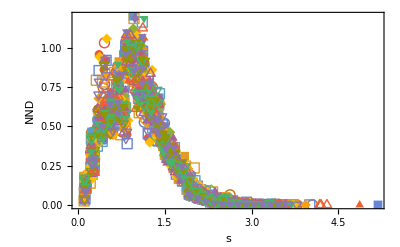

```mathematica
plotNND=ListPlot[Import[#,"Data"]&/@filesNND,PlotMarkers->Automatic, Frame->True,FrameLabel->{Style["s",FontFamily->"Times New Roman",Italic,15],Style["NND",FontFamily->"Times New Roman",Italic,15]}]
```

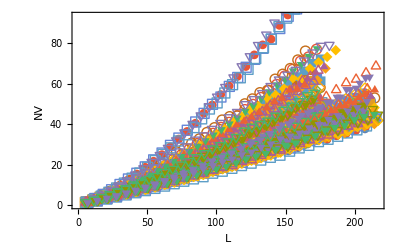

```mathematica
plotNV=ListPlot[Import[#,"Data"]&/@filesNV,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["L",FontFamily->"Times New Roman",Italic,15],Style["NV",FontFamily->"Times New Roman",Italic,15]}]
```